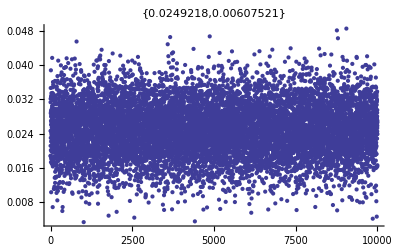

```mathematica
size = ReadList["/tmp/gaussian_dropsize",Number];
ListPlot[size, PlotLabel->{Mean[size],StandardDeviation[size]}]
```

```mathematica
position = ReadList["/tmp/gaussian_dropposition",{Number, Number, Number}];
ListPointPlot3D[position,ColorFunction->"Rainbow", PlotStyle->PointSize[Large]]
```

-Graphics3D-

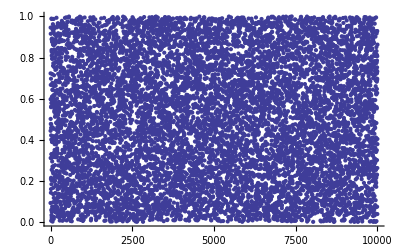

0.500038

0.290184

```mathematica
gauss = ReadList["/tmp/random_uniform",Number];
ListPlot[gauss]
Mean[gauss]
StandardDeviation[gauss]
```

```mathematica
??Large
```

Large is a style or option setting that specifies that objects should be large.

Attributes[Large]={Protected}